```mathematica
kinfr=0.1570/0.2
```

0.785

```mathematica
kinfc=0.1570/0.1532
```

1.0248

```mathematica
l2r=1/(3*0.0362*0.2)
```

46.0405

```mathematica
l2c=1/(3*0.1532*0.0362)
```

60.1051

```mathematica
r=200
```

200

```mathematica
h=400
```

400

```mathematica
bc2=(kinfc-1)/l2c-(2.405/r)^2
```

0.000268079

```mathematica
br2=(kinfr-1)/l2r-(2.405/r)^2
```

-0.0048144

```mathematica
yr2=-br2
```

0.0048144

```mathematica
dc=1/(3*0.0362)
```

9.2081

```mathematica
bc=bc2^0.5
```

0.0163731

```mathematica
yr=yr2^0.5
```

0.0693859

```mathematica
FindRoot[(1/bc)*Tan[bc*height]==-Tanh[yr*(h-height)]/yr,{height,300}]
```

{height→370.016}

```mathematica
FindRoot[(1/bc)*Tan[bc*height]==-Tanh[yr*(h-height)]/yr,{height,200}]
```

```mathematica
{height->177.72165511888016}
```

{height→177.722}

```mathematica
height=177.722;
```

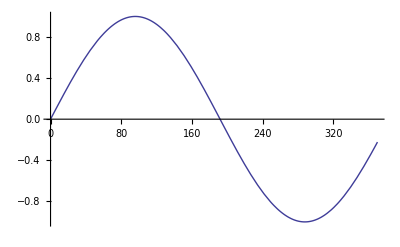

```mathematica
Plot[Sin[bc*z],{z,0,370.016}]
```

```mathematica
σap2=0.1570-dc*(((2.405/200)^2)+((Pi/400)^2))
```

0.155101

```mathematica
σab=0.155101-0.1532
```

0.001901

```mathematica
volume=Pi*(200^2)*400.0
```

5.02655×10^7

```mathematica
numberdensity=σab/(755*10^-24)
```

2.51788×10^18

```mathematica
atoms=numberdensity*volume
```

1.26562×10^26

```mathematica
massboron=atoms*(10.81)/(6.022*10^23)
```

2271.9

```mathematica
z=(Pi/2.)/bc
```

95.9375

```mathematica
a=Sin[bc*height]/(Sinh[yr*(h-height)])
```

9.20469×10^-8

```mathematica
int1=Integrate[Sinh[yr(h-paul)],{paul,height,h}]
```

3.59585×10^7

```mathematica
int2=Integrate[Sin[bc*paul],{paul,0,height}]
```

120.519

```mathematica
pfavg=int2/height+(a*int1)/(h-height)
```

0.693022

```mathematica
ppf=1/pfavg
```

1.44296

```mathematica
Pi/2.
```

1.5708